```mathematica
MySuffix="-dd";
MySuffix="";
```

## Initialization

### Packages, Paths, common options

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}];
If[FileExistsQ["~/home-uni/algebra/packages"],BaseDir="~/home-uni",BaseDir="~/uni"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;
<<GlbPlots.m;

(* Taken from http://forums.wolfram.com/mathgroup/archive/1999/Apr/msg00028.html (slightly modified) *)
JHEPPlot[grObj_Graphics]:=Module[{fulopts,tcklst,th=0.004},
fulopts=FullOptions[grObj];
tcklst=FrameTicks/.fulopts/.{loc_,lab_,len:{_,_},{sty:___}}:>{loc,lab,2*len,{Directive[sty,Thickness[th]]}};
grObj/.Graphics[prims_,(opts__)?OptionQ]:>Graphics[prims,FrameTicks->tcklst,FrameTicksStyle->Thickness[th],FrameStyle->Thickness[th],opts]
];

KPImport[file_String,opts___]:=Module[{},
(*If[AbsoluteTime[FileDate[file]]<AbsoluteTime[{2013,3,7}],
Print[Style["Warning: File "<>file<>" is older than March 7, 2012!",FontColor->Red]];
];*)
Return[Import[file,opts]];
];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### Reading GLoBES event rate files

```mathematica
glbSignalTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,Plus@@Data⟦1,All,All,2⟧}];
glbBGTot[Data_List]:=Transpose[{Data⟦2,1,All,1⟧,Plus@@Data⟦2,All,All,2⟧}];
glbSignalBGTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,(Plus@@Data⟦1,All,All,2⟧)+(Plus@@Data⟦2,All,All,2⟧)}];
```

## MiniBooNE

### Covariance Matrix

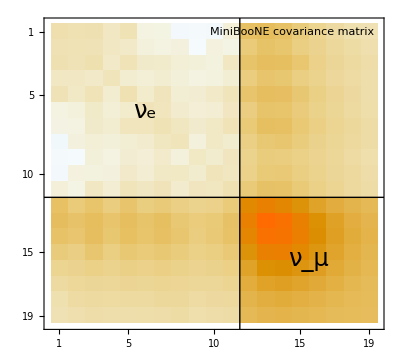

```mathematica
DataFilesCov={"default"}/.s_String:>"3-3p1/mbbg/dm41s22thmueUm4-mbjk-cov-"<>s<>".dat";
For[i=1,i≤1+0Length[DataFilesCov],i++,
DataCov[i]=Import[DataFilesCov⟦i⟧,"Table"];
McovInv[i]=Cases[DataCov[i],{"#","McovInv",x__}:>{x}];
McovInv[i]=McovInv[i]⟦1;;Length[McovInv[i]]/2⟧; (* covariance matrix appears twice in the files, cut away the 2nd occurrence *)
MyMcovPlot[i]=Overlay[{MatrixPlot[Inverse[McovInv[i]]⟦1;;19,1;;19⟧,PlotLegends->Automatic,
(*Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},*)
Epilog->{
Line[{{11,-1},{11,100}}],
Line[{{-1,19-11},{100,19-11}}],
Text[Style["ν_e",FontSize->24],{5.5,19-5.5}],
Text[Style["ν_μ",FontSize->24],{11+4,19-11-4}],
Text[Framed["MiniBooNE covariance matrix"],Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]
}](*,Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]*)},Alignment->{0.9,1}];
];
Grid[{{MyMcovPlot[1]}}]
Export["fig/mb-cov-matrix.pdf",MyMcovPlot[1]];
```

### Spectra

```mathematica
(* Read MiniBooNE data *)
Clear[DataMB];
DataFilesMB={"0-code/glb/mb-jk-2018/miniboone_nuedata_lowe.txt"};
DataFilesMBBG={"0-code/glb/mb-jk-2018/miniboone_nuebgr_lowe.txt"};
DataFilesMBBGStacked={"0-code/glb/mb-jk-2018/mb-all-bg-1805.12028.dat"};
DataFilesMBbar={"0-code/glb/mb-jk-2018/miniboone_nuebardata_lowe.txt"};
DataFilesMBbarBG={"0-code/glb/mb-jk-2018/miniboone_nuebarbgr_lowe.txt"};
DataFilesMBbarBGStacked={"0-code/glb/mb-jk-2018/mb-all-bg-nubarmode-1805.12028.dat"};
DataFilesMBmu={"0-code/glb/mb-jk-2018/miniboone_numudata.txt"};
DataFilesMBmuPred={"0-code/glb/mb-jk-2018/miniboone_numu.txt"};
DataFilesMBmubar={"0-code/glb/mb-jk-2018/miniboone_numubardata.txt"};
DataFilesMBmubarPred={"0-code/glb/mb-jk-2018/miniboone_numubar.txt"};
BinBoundaries0=Flatten[Import["0-code/glb/mb-jk-2018/miniboone_binboundaries_nue_lowe.txt","Table"]]MeV//.NN;
BinWidths0=Differences[BinBoundaries0];
BinCenters0=ListConvolve[{0.5,0.5},BinBoundaries0];
BinBoundariesMu0=Flatten[Cases[Import["0-code/glb/mb-jk-2018/miniboone_binboundaries_numu.txt","Table"],{_?NumericQ}]]MeV//.NN;
BinWidthsMu0=Differences[BinBoundariesMu0];
BinCentersMu0=ListConvolve[{0.5,0.5},BinBoundariesMu0];
BGStyles={Null,
{Directive[Thin,Black],GrayLevel[.6]},
{Directive[Thin,Black],RGBColor[0.529,0.4,0.341]},
{Directive[Thin,Black],RGBColor[0.867,0.729,0.529]},
{Directive[Thin,Black],RGBColor[0.812,0.373,0.38]},
{Directive[Thin,Black],RGBColor[0.518,0.761,0.639]},
{Directive[Thin,Black],RGBColor[0.690,0.812,0.78]}
}/.{RGBColor[c__]:>Lighter[RGBColor[c]],GrayLevel[c__]:>Lighter[GrayLevel[c]]};
For[i=1,i≤Length[DataFilesMB],i++,
BinBoundaries[i]=BinBoundaries0;
BinWidths[i]=BinWidths0;
BinCenters[i]=BinCenters0;
DataMB[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMB⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBBGStacked[i]=Cases[Import[DataFilesMBBGStacked⟦i⟧,"Table"],{Repeated[_?NumericQ]}]*MeV^-1//.NN;
DataMBBG[i]=Differences/@(ReplacePart[#,1->0.]&/@DataMBBGStacked[i]⟦All,1;;7⟧);
MBSystUpperInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-2⟧,DataMBBGStacked[i]⟦1,-2⟧]}//.NN],InterpolationOrder->0];
MBSystLowerInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-1⟧,DataMBBGStacked[i]⟦1,-1⟧]}//.NN],InterpolationOrder->0];
MBSystCenterInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-3⟧,DataMBBGStacked[i]⟦1,-3⟧]}//.NN],InterpolationOrder->0];

BinBoundariesMu[i]=BinBoundariesMu0;
BinWidthsMu[i]=BinWidthsMu0;
BinCentersMu[i]=BinCentersMu0;
DataMBmu[i]=Transpose[{BinCentersMu0,Flatten[Cases[Import[DataFilesMBmu⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBmuPred[i]=Transpose[{BinCentersMu0,Flatten[Cases[Import[DataFilesMBmuPred⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]/BinWidthsMu0}];

PlotListObs[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/MeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/MeV^-1]}//.NN&,{DataMB[i],BinWidths[i]}];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black]];
MyPlotMBBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[i]/GeV,Append[DataMBBGStacked[i]⟦All,j⟧,DataMBBGStacked[i]⟦-1,j⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->BGStyles⟦j,1⟧,Filling->{1->{Bottom,Lighter[BGStyles⟦j,2⟧]}}],{j,Length[DataMBBGStacked[i]⟦1⟧]-2,2,-1}]];

PlotListObsMu[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/MeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/MeV^-1]}//.NN&,{DataMBmu[i],BinWidthsMu[i]}];
MyPlotObsMu[i]=ErrorListPlot[PlotListObsMu[i],PlotRange->All,PlotStyle->Directive[Thick,Black]];
MyPlotMBmuPred[i]=ListPlot[Transpose[{BinBoundariesMu[i]/GeV,Append[DataMBmuPred[i]⟦All,2⟧,DataMBmuPred[i]⟦-1,2⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->Directive[Thin,Black],Filling->{1->{Bottom,RGBColor[1,.9,1]}}]
];
```

```mathematica
(* Read spectrum from Joachim's code *)
MyTunes={"default-nobgosc","default","default",
"gibuu-brscan-min","gibuu-brscan-max","gibuu","nuance","nuwro", (* make sure "gibuu" appears after "gibuu-brscan-*" *)
"G18_01a_02_11a","G18_01b_02_11a","G18_02a_02_11a","G18_02b_02_11a","G18_10a_02_11a","G18_10b_02_11a"};
MyTunesHumanReadable={"MB fit (w/o BG osc.)","MB fit (with BG osc.)","MB fit (w/ BG osc.)",
"GiBUU (Δ→γ -2σ)","GiBUU (Δ→γ +2σ)",Style["GiBUU\n(Δ→γ only, BR ±2σ)",TextAlignment->Left,LineSpacing->0.9,FontSize->14],"NUANCE","NuWro",
"GENIE G18_01a_02_11a","GENIE G18_01b_02_11a","GENIE G18_02a_02_11a","GENIE G18_02b_02_11a","GENIE G18_10a_02_11a","GENIE G18_10b_02_11a"};
MyTuneColors={RGBColor[0,0,1],RGBColor[0,0,1],RGBColor[0,0,1],
RGBColor[0,0,.7],RGBColor[0,0,.7],RGBColor[0,0,.7],RGBColor[.7,0,.7],RGBColor[.7,.7,0],
RGBColor[1,0,0],RGBColor[1,0.110,0],RGBColor[1,0.220,0],RGBColor[1,0.0333,0],RGBColor[1,0.443,0],RGBColor[1,0.557,0]};
MyTuneLineStyles={Dashed,Dashing[{}],Dashing[{}],
Dashed,Dotted,Dashing[{}],Dashing[{}],Dashing[{}],
Dashing[{}],Dashed,DotDashed,Dotted,Dashing[{}],Dashed};
If[MySuffix=="-dd", (* don't show GiBUU lines for data-driven backgrounds - they are unreliable due to GiBUU's π^0 problem *)
ii=Flatten[Position[StringMatchQ[MyTunes,RegularExpression["gibuu.*"]],False]];
MyTunes=MyTunes⟦ii⟧;
MyTunesHumanReadable=MyTunesHumanReadable⟦ii⟧;
MyTuneColors=MyTuneColors⟦ii⟧;
MyTuneLineStyles=MyTuneLineStyles⟦ii⟧;
];

DataFiles=MyTunes/.s_String:>"3-3p1/mbbg/dm41s22thmueUm4-mbjk-"<>s<>MySuffix<>".dat";
MyStyles={Directive[Thick,Dashed,Black],Directive[Thick,Blue]};
For[i=1,i≤Length[DataFiles],i++,
(* extract chi^2 values *)
DataRaw[i]=Import[DataFiles⟦i⟧,"Table"];
DataChi2[i]=Cases[DataRaw[i],{"#","CHI2",x_}:>x];
Chi2BF[i]=DataChi2[i]⟦-1⟧;
Chi2NoOsc[i]=Min[Cases[DataRaw[i],{Repeated[_?NumericQ]}]⟦1,{-2,-1}⟧]; (* 1st data line = smallest parameter values = no osc. *)

(* extract signal and background spectra *)
DataJK[i]=Cases[DataRaw[i],{"#","MBJKSPECT",x__}:>{x}];
DataJK[i]=Partition[DataJK[i],2*Length[BinWidths[1]]+Length[BinWidthsMu[1]]+1]; (* each block contains 11 signal entries for Subscript[ν, e], 8 entries for Subscript[ν, μ], 11 background entries, 1 params entry *)
DataJKspect[i]=DataJK[i]⟦All,1;;Length[BinWidths[1]]⟧;
DataJKbg[i]=(Cases[#,{"BG",__}]&/@DataJK[i])⟦All,All,2;;⟧;
DataJKmu[i]=(Cases[#,{"MU",__}]&/@DataJK[i])⟦All,All,2;;⟧;

(* extract parameter values *)
DataParams[i]=DataJK[i]⟦All,-1,2;;⟧;
DM41BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"DM41",x_}:>x]⟦1⟧;
s22thmueBF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"s22thmue",x_}:>x]⟦1⟧;
Uμ4BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"Um4",x_}:>x]⟦1⟧;
Ue4BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"Ue4",x_}:>x]⟦1⟧;
];
```

```mathematica
(* Plot spectra *)
For[i=1,i≤Length[DataFiles],i++,
(* choose parameter point at which to extract rates *)

(* i=3: bfp from our full MB fit; otherwise results at individual bfp *)
(*Switch[i,
3,(jj=Flatten[Position[DataParams[i],{__,"DM41",DM41BF[2],__,"s22thmue",s22thmueBF[2],___}]];
jj=jj⟦Ordering[DataChi2[i]⟦jj⟧,1]⟧⟦1⟧); (* extract rates at bfp of "classical" MB fit *),
_,jj=Length[DataParams[i]]; (* extract rates at best fit point *)
];*)

(* extract rates at specific parameters *)
(*(jj=Flatten[Position[DataParams[i],{__,"DM41",_?(#>0.7&&#<0.9&),__,"s22thmue",_?(#<0.0002&),___}]];
jj=jj⟦Ordering[DataChi2[i]⟦jj⟧]⟦1⟧⟧); *)

(* extract rates at first point in file ≃ no oscillations *)
(*jj=1; *)

(* extract rates at best fit point *)
jj=Length[DataParams[i]];

DM41[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"DM41",x_}:>x]⟦1⟧;
s22thmue[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"s22thmue",x_}:>x]⟦1⟧;
Uμ4[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"Um4",x_}:>x]⟦1⟧;
Ue4[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"Ue4",x_}:>x]⟦1⟧;
Chi2[i]=DataChi2[i]⟦jj⟧;

(* extract signal and background rates *)
EventsSignal[i]=Transpose[{BinCenters[1],DataJKspect[i]⟦jj,All,1⟧}];
EventsBG[i]=Transpose[{BinCenters[1],DataJKspect[i]⟦jj,All,2⟧}];
EventsBGefromμ[i]=Transpose[{BinCenters[1],DataJKbg[i]⟦jj,All,2⟧}];
EventsBGefromK[i]=Transpose[{BinCenters[1],DataJKbg[i]⟦jj,All,3⟧}];
EventsBGother[i]=Transpose[{BinCenters[1],DataJKbg[i]⟦jj,All,1⟧}];
EventsTotal[i]=Transpose[{BinCenters[1],Total/@DataJKspect[i]⟦jj,All,{1,2}⟧}];
EventsMu[i]=Transpose[{BinCentersMu[1],DataJKmu[i]⟦jj,All,1⟧}];
EventsMuBar[i]=Transpose[{BinCentersMu[1],DataJKmu[i]⟦jj,All,2⟧}];

(* create data for stacked background histogram *)
EventsBGStacked[i]=Flatten[{#⟦1⟧,Accumulate[#⟦2;;⟧]}]&/@Transpose[{
BinCenters[1],
EventsBGother[i]⟦All,2⟧*DataMBBG[1]⟦All,1⟧/(Total/@DataMBBG[1]⟦All,1;;4⟧+1*^-100), (* "other" backgrounds *)
EventsBGother[i]⟦All,2⟧*DataMBBG[1]⟦All,2⟧/(Total/@DataMBBG[1]⟦All,1;;4⟧+1*^-100), (* dirt background *)
EventsBGother[i]⟦All,2⟧*DataMBBG[1]⟦All,3⟧/(Total/@DataMBBG[1]⟦All,1;;4⟧+1*^-100), (* Δ background *)
EventsBGother[i]⟦All,2⟧*DataMBBG[1]⟦All,4⟧/(Total/@DataMBBG[1]⟦All,1;;4⟧+1*^-100), (* π^0 background *)
EventsBGefromK[i]⟦All,2⟧, (* Subscript[ν, e] from K background *)
EventsBGefromμ[i]⟦All,2⟧ (* Subscript[ν, e] from μ background *)
}];

(* make plot of total rate (sig+bg) - neutrino mode *)
EventsTotalInterpol[i]=Interpolation[Transpose[{BinBoundaries[1],
Prepend[EventsTotal[i]⟦All,-1⟧/BinWidths[1],EventsTotal[i]⟦1,-1⟧/BinWidths[1]⟦-1⟧]}//.NN],InterpolationOrder->0];
PlotListTotal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsTotal[i],EventsTotal[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
If[MyTunes⟦i⟧=="gibuu", (* for GiBUU, plot also band indicating min/max radiative BR *)
imax=Position[MyTunes,"gibuu-brscan-max"]⟦1,1⟧;
imin=Position[MyTunes,"gibuu-brscan-min"]⟦1,1⟧;
MyPlotTotal[i]=Show[ListPlot[{PlotListTotal[i],PlotListTotal[imin],PlotListTotal[imax]},InterpolationOrder->0,Joined->True,PlotStyle->{Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧],None,None},Filling->{2->{{3},RGBColor[.5,.5,1,.5]}}]],
(* Else *)
MyPlotTotal[i]=Show[ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧]]]
];

PlotListMu[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundariesMu[1],Append[EventsMu[i],EventsMu[i]⟦-1⟧],Append[BinWidthsMu[1],BinWidthsMu[1]⟦-1⟧]}];
If[MyTunes⟦i⟧=="gibuu", (* for GiBUU, plot also band indicating min/max radiative BR *)
MyPlotMu[i]=ListPlot[{PlotListMu[i],PlotListMu[imin],PlotListMu[imax]},InterpolationOrder->0,Joined->True,PlotStyle->{Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧],None,None},Filling->{2->{{3},RGBColor[.5,.5,1,.5]}}],
(* Else *)
MyPlotMu[i]=ListPlot[PlotListMu[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧]];
];

(* make stacked background plot *)
If[MyTunes⟦i⟧=="default-nobgosc",
MyPlotBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[1]/GeV,Append[EventsBGStacked[i]⟦All,j⟧/BinWidths[1],EventsBGStacked[i]⟦-1,j⟧/BinWidths[1]⟦-1⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->Directive[Darker[BGStyles⟦j,2⟧],Thick,Dotted]],{j,Length[EventsBGStacked[i]⟦1⟧],2,-1}]],
(* Else *)
MyPlotBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[1]/GeV,Append[EventsBGStacked[i]⟦All,j⟧/BinWidths[1],EventsBGStacked[i]⟦-1,j⟧/BinWidths[1]⟦-1⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->BGStyles⟦j,1⟧,Filling->{1->{Bottom,BGStyles⟦j,2⟧}}],{j,Length[EventsBGStacked[i]⟦1⟧],2,-1}]]
];
];
```

```mathematica
(* make plot illustrating the systematic uncertainty on (sig+bg) - neutrino mode *)
i=2;
MyPlotSyst[i]=RegionPlot[MBSystLowerInterpol[x GeV]<y/MeV-EventsTotalInterpol[i][x GeV]+MBSystCenterInterpol[x GeV]<MBSystUpperInterpol[x GeV]//.NN,Evaluate[{x,BinBoundaries[1]⟦1⟧/GeV,BinBoundaries[1]⟦-1⟧/GeV}//.NN],{y,0,6},PlotPoints->200,Mesh->150,MeshFunctions->{#1-#2&},BoundaryStyle->None,MeshStyle->Directive[GrayLevel[.6],Thickness[.002]],PlotStyle->GrayLevel[0,.1]];
```

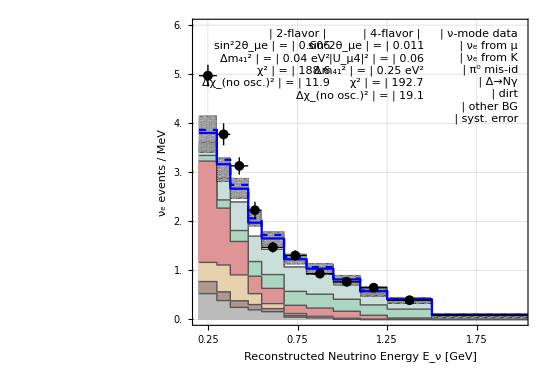
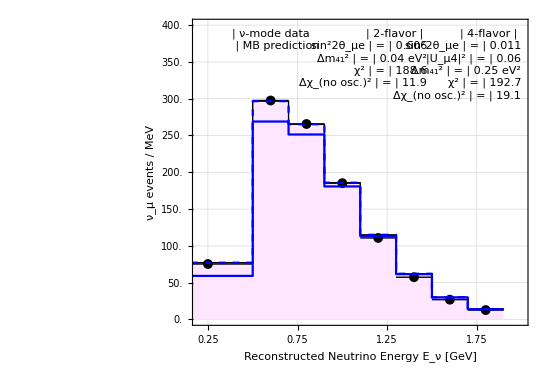
-Graphics-Brdar Kopp 2021 | -Graphics-Brdar Kopp 2021

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyLegend1[i]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"ν-mode data"},
{LegendBox[BGStyles⟦7,2⟧,BGStyles⟦7,1⟧],"ν_e from μ"},
{LegendBox[BGStyles⟦6,2⟧,BGStyles⟦6,1⟧],"ν_e from K"},
{LegendBox[BGStyles⟦5,2⟧,BGStyles⟦5,1⟧],"π^0 mis-id"},
{LegendBox[BGStyles⟦4,2⟧,BGStyles⟦4,1⟧],"Δ→Nγ"},
{LegendBox[BGStyles⟦3,2⟧,BGStyles⟦3,1⟧],"dirt"},
{LegendBox[BGStyles⟦2,2⟧,BGStyles⟦2,1⟧],"other BG"},
{Show[LegendBox[GrayLevel[0,.1]],RegionPlot[True,{x,0,1},{y,0,1},Mesh->6,MeshFunctions->{#1-2#2&},BoundaryStyle->None,MeshStyle->Directive[Black,Thickness[.007]],PlotStyle->Transparent]],"syst. error"}
},ItemSize->{Automatic,1.3},Spacings->{Automatic,0}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegendMu[i]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"ν-mode data"},
{LegendBox[RGBColor[1,.9,1],Directive[Thin,Black]],"MB prediction"}
},ItemSize->{Automatic,1.3},Spacings->{Automatic,0}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend2[i]=Framed[Grid[DeleteMissing[{
{LegendLine[Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧,Thick]],If[i==1,"2-flavor","4-flavor"],SpanFromLeft},
{"sin^22θ_μe","=",ToString[Round[s22thmue[i],0.001]]},
If[i==1,Missing[],{"|U_μ4|^2","=",ToString[Round[Uμ4[i]^2,0.01]]}],
{"Δm_41^2","=",ToString[Round[DM41[i],0.01]]<> " eV^2"},
{"χ^2","=",ToString[Round[Chi2[i],0.1]]},
{"Δχ_(no osc.)^2","=",ToString[Round[Chi2NoOsc[i]-Chi2[i],0.1]]}
}],ItemSize->{Automatic,1.3}, Spacings->{0.3,{0,2->0.3}},Alignment->{{Right,Center,Left},Baseline,{1,1}->Center},BaseStyle->{FontSize->15},Dividers->{False,{False,2->True}}],Background->RGBColor[1,1,1,.8]];
];
i=2;
MyPlot[i]=Overlay[{JHEPPlot[Show[
MyPlotBGStacked[2],MyPlotSyst[2],MyPlotTotal[1],MyPlotTotal[2],MyPlotObs[1],
PlotRange->{{0.2,2.},{0,6.0}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","ν_e events / MeV"},
Epilog->{
Inset[MyLegend1[i],Scaled[{0.97,0.97}],{1,1}],
Inset[MyLegend2[1],Scaled[{0.41,0.97}],{1,1}],
Inset[MyLegend2[2],Scaled[{0.69,0.97}],{1,1}]
(*Text[Framed[MyTunesHumanReadable⟦i⟧],Scaled[{0.02,0.97}],{-1,1},Background->GrayLevel[1,.7]]*)
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
MyPlot[100+i]=Overlay[{JHEPPlot[Show[
MyPlotMBmuPred[1],MyPlotObsMu[1],MyPlotMu[1],MyPlotMu[2],
PlotRange->{{0.2,2.},{0,400.}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","ν_μ events / MeV"},
Epilog->{
Inset[MyLegendMu[1],Scaled[{0.117,0.97}],{-1,1}],
Inset[MyLegend2[1],Scaled[{0.70,0.97}],{1,1}],
Inset[MyLegend2[2],Scaled[{0.98,0.97}],{1,1}]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
Grid[{{MyPlot[2],MyPlot[102]}}]
Export["fig/mb-spectrum-nue-default.pdf",MyPlot[2]];
Export["fig/mb-spectrum-numu-default.pdf",MyPlot[102]];
```

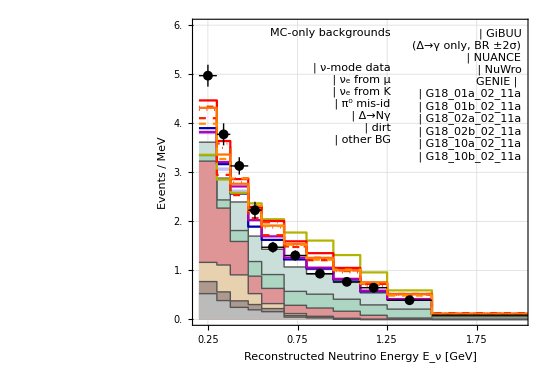
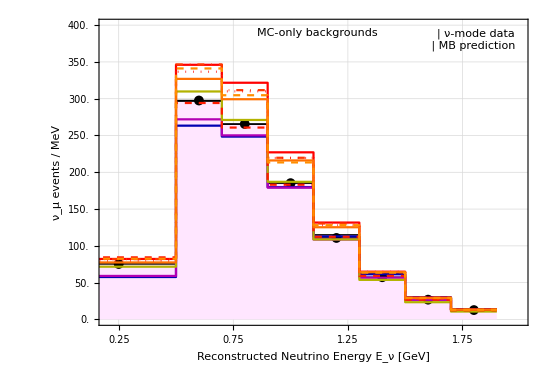
-Graphics-Brdar Kopp 2021 | -Graphics-Brdar Kopp 2021

```mathematica
MyLegend1[1]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"ν-mode data"},
{LegendBox[BGStyles⟦7,2⟧,BGStyles⟦7,1⟧],"ν_e from μ"},
{LegendBox[BGStyles⟦6,2⟧,BGStyles⟦6,1⟧],"ν_e from K"},
{LegendBox[BGStyles⟦5,2⟧,BGStyles⟦5,1⟧],"π^0 mis-id"},
{LegendBox[BGStyles⟦4,2⟧,BGStyles⟦4,1⟧],"Δ→Nγ"},
{LegendBox[BGStyles⟦3,2⟧,BGStyles⟦3,1⟧],"dirt"},
{LegendBox[BGStyles⟦2,2⟧,BGStyles⟦2,1⟧],"other BG"}
(*{Show[LegendBox[GrayLevel[0,.1]],RegionPlot[True,{x,0,1},{y,0,1},Mesh->6,MeshFunctions->{#1-2#2&},BoundaryStyle->None,MeshStyle->Directive[Black,Thickness[.007]],PlotStyle->Transparent]],"syst. error"}*)
},ItemSize->{Automatic,1.3},Spacings->{Automatic,0}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
ll=Flatten[Position[MyTunes,"gibuu"|"nuance"|"nuwro"]];
MyLegend1[2]=Framed[Grid[{
Sequence@@Table[{If[MyTunes⟦i⟧=="gibuu",
LegendBand[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧],RGBColor[.5,.5,1,.5]],
(* Else *)
LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧]]
],MyTunesHumanReadable⟦i⟧},{i,ll}],
{Style["GENIE",Bold],SpanFromLeft},
Sequence@@Table[{LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧]],StringReplace[MyTunesHumanReadable⟦i⟧,"GENIE ":>""]},{i,ll⟦-1⟧+1,Length[DataFiles]}]
},ItemSize->{Automatic,1.3},Spacings->{Automatic,{0,(Length[ll]+1)->0.4}}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend2[i]=Framed[Grid[{
{"sin^22θ_μe","=",ToString[Round[s22thmue[i],0.001]]},
{"|U_μ4|^2","=",ToString[Round[Uμ4[i]^2,0.0001]]},
{"m_4","=",ToString[Round[Sqrt[N[DM41[i]]]]]<> " eV^2"}
},ItemSize->{Automatic,1.3}, Spacings->{0.3,0},Alignment->{{Right,Center,Left},Baseline},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyPlot[1]=Overlay[{JHEPPlot[Show[
MyPlotBGStacked[2],(*MyPlotSyst[2],*)Sequence@@Table[MyPlotTotal[i],{i,ll}],Sequence@@Table[MyPlotTotal[i],{i,ll⟦-1⟧+1,Length[DataFiles]}],MyPlotObs[1],
PlotRange->{{0.2,2.},{0,6.0}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","Events / MeV"},
Epilog->{
Inset[MyLegend1[1],Scaled[{0.59,0.86}],{1,1}],
Inset[MyLegend1[2],Scaled[{0.98,0.97}],{1,1}],
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven backgrounds","MC-only backgrounds"]],Scaled[{0.59,0.97}],{1,1},Background->GrayLevel[1,.7]]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
MyPlot[101]=Overlay[{JHEPPlot[Show[
MyPlotMBmuPred[1],MyPlotObsMu[1],Sequence@@Table[MyPlotMu[i],{i,ll}],Sequence@@Table[MyPlotMu[i],{i,ll⟦-1⟧+1,Length[DataFiles]}],
PlotRange->{{0.2,2.},{0,400.}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","ν_μ events / MeV"},
Epilog->{
Inset[MyLegendMu[1],Scaled[{0.97,0.97}],{1,1}],
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven backgrounds","MC-only backgrounds"]],Scaled[{0.65,0.97}],{1,1},Background->GrayLevel[1,.7]]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
Grid[{{MyPlot[1],MyPlot[101]}}]
OutputSuffix=If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"dd","fp"];
Export["fig/mb-spectrum-nue-comparison-"<>OutputSuffix<>".pdf",MyPlot[1]];
Export["fig/mb-spectrum-numu-comparison-"<>OutputSuffix<>".pdf",MyPlot[101]];
```

```mathematica
i=6;
DM41[i]
s22thmue[i]
Uμ4[i]
```

0.251189

0.0104383

0.270252

### Exclusion Regions in sin^2 2 θ_μe and Δm^2

```mathematica
MyTunes={"default","default-nobgosc",
"gibuu","gibuu-brscan-min","gibuu-brscan-max","nuance","nuwro",
"G18_01a_02_11a","G18_01b_02_11a","G18_02a_02_11a","G18_02b_02_11a","G18_10a_02_11a","G18_10b_02_11a"};
MyTunesHumanReadable={"MB prediction","MB prediction (no BG osc)",
"GiBUU (Δ→γ only)","GiBUU (BR -2σ)","GiBUU (BR +2σ)","NUANCE","NuWro",
"GENIE G18_01a_02_11a","GENIE G18_01b_02_11a","GENIE G18_02a_02_11a","GENIE G18_02b_02_11a","GENIE G18_10a_02_11a","GENIE G18_10b_02_11a"};
MyTuneColors={RGBColor[0,0,1],RGBColor[0,0,1],
RGBColor[0,0,.7],RGBColor[0,0,.7],RGBColor[0,0,.7],RGBColor[.7,0,.7],RGBColor[.7,.7,0],
RGBColor[1,0,0],RGBColor[1,0.110,0],RGBColor[1,0.220,0],RGBColor[1,0.0333,0],RGBColor[1,0.443,0],RGBColor[1,0.557,0]};
MyTuneLineStyles={Dashing[{}],Dashed,
Dashing[{}],Dashed,Dotted,Dashing[{}],Dashing[{}],
Dashing[{}],Dashed,DotDashed,Dotted,Dashing[{}],Dashed,
Dashing[{}],Dashing[{}]};
If[MySuffix=="-dd", (* don't show GiBUU lines for data-driven backgrounds - they are unreliable due to GiBUU's π^0 problem *)
ii=Flatten[Position[StringMatchQ[MyTunes,RegularExpression["gibuu.*"]],False]];
MyTunes=MyTunes⟦ii⟧;
MyTunesHumanReadable=MyTunesHumanReadable⟦ii⟧;
MyTuneColors=MyTuneColors⟦ii⟧;
MyTuneLineStyles=MyTuneLineStyles⟦ii⟧;
];

DataFiles="3-3p1/mbbg/dm41s22thmueUm4-mbjk-"<>#<>MySuffix<>".dat"&/@MyTunes;
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=KPImport[DataFiles⟦i⟧,"Table"];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]=Select[Data[i],#⟦3⟧<0.75&]; (* select Subscript[U, μ4] range to avoid solutions with Subscript[U, μ4]~1 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[10^(#⟦2⟧)/(4*(10^(#⟦3⟧))^2)>0.2,1.*^12,#⟦4⟧]}&/@Data[i]; (* restrict Subscript[U, e4] range *)
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
(*Data[i]=Select[#,#⟦3⟧==-1.0&]⟦1,{1,2,4}⟧&/@Data[i], (* select specific Subscript[U, μ4] *)*)
jj=Ordering[#⟦All,-1⟧,1]&/@Data[i];
DataUμ4[i]=MapThread[Flatten[{#1⟦1,1⟧,#1⟦1,2⟧,#1⟦#2,3⟧}]&,{Data[i],jj}]; (* save optimum Subscript[U, μ4] at each grid point in (s22thmue,dm41) *)
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Data[i], (* save χ^2 at optimum Subscript[U, μ4] *)

(* Else - data files in dm41, th14, th24 *)
Print["Wrong file format!"];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
logs22thMin[i]=Min[Data[i]⟦All,2⟧];
logs22thMax[i]=Max[Data[i]⟦All,2⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataUμ4Interpol[i]=Interpolation[DataUμ4[i],InterpolationOrder->1];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
]; (* End[if] *)

Print[DataFiles⟦i⟧];
Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],logs22thMin[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

3-3p1/mbbg/dm41s22thmueUm4-mbjk-default.dat

Best fit: sin^22θ_μe=1/100, Δm^2=0.251189

χ_min^2=192.7, χ_(no osc)^2=211.77, Δχ_(no osc.)^2=19.0691 (CL 0.999928)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-default-nobgosc.dat

Best fit: sin^22θ_μe=0.501187, Δm^2=0.0398107

χ_min^2=188.602, χ_(no osc)^2=200.489, Δχ_(no osc.)^2=11.8875 (CL 0.997378)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-gibuu.dat

Best fit: sin^22θ_μe=1/100, Δm^2=0.251189

χ_min^2=192.211, χ_(no osc)^2=216.767, Δχ_(no osc.)^2=24.5565 (CL 0.999995)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-gibuu-brscan-min.dat

Best fit: sin^22θ_μe=0.00630957, Δm^2=0.316228

χ_min^2=194.416, χ_(no osc)^2=222.496, Δχ_(no osc.)^2=28.0805 (CL 0.999999)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-gibuu-brscan-max.dat

Best fit: sin^22θ_μe=0.00501187, Δm^2=0.316228

χ_min^2=192.075, χ_(no osc)^2=213.219, Δχ_(no osc.)^2=21.1441 (CL 0.999974)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-nuance.dat

Best fit: sin^22θ_μe=0.00794328, Δm^2=0.316228

χ_min^2=196.948, χ_(no osc)^2=216.295, Δχ_(no osc.)^2=19.3474 (CL 0.999937)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-nuwro.dat

Best fit: sin^22θ_μe=0.00199526, Δm^2=3.16228

χ_min^2=219.354, χ_(no osc)^2=234.964, Δχ_(no osc.)^2=15.6099 (CL 0.999592)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_01a_02_11a.dat

Best fit: sin^22θ_μe=0.0794328, Δm^2=0.125893

χ_min^2=195.399, χ_(no osc)^2=216.955, Δχ_(no osc.)^2=21.5561 (CL 0.999979)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_01b_02_11a.dat

Best fit: sin^22θ_μe=1/10000, Δm^2=0.794328

χ_min^2=195.458, χ_(no osc)^2=211.593, Δχ_(no osc.)^2=16.1351 (CL 0.999686)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_02a_02_11a.dat

Best fit: sin^22θ_μe=0.0501187, Δm^2=0.125893

χ_min^2=192.682, χ_(no osc)^2=207.821, Δχ_(no osc.)^2=15.1382 (CL 0.999484)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_02b_02_11a.dat

Best fit: sin^22θ_μe=0.0501187, Δm^2=0.125893

χ_min^2=194.236, χ_(no osc)^2=209.246, Δχ_(no osc.)^2=15.0099 (CL 0.99945)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_10a_02_11a.dat

Best fit: sin^22θ_μe=0.0158489, Δm^2=0.251189

χ_min^2=193.756, χ_(no osc)^2=204.92, Δχ_(no osc.)^2=11.1639 (CL 0.996235)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_10b_02_11a.dat

Best fit: sin^22θ_μe=0.0125893, Δm^2=0.398107

χ_min^2=192.915, χ_(no osc)^2=210.84, Δχ_(no osc.)^2=17.9254 (CL 0.999872)

```mathematica
Print["suffix = ",MySuffix];
ss="";
For[i=1,i≤Length[DataFiles],i++,
If[i==2,Continue[]];
s=ToString[SetPrecision[10^BFP[i]⟦1⟧,2]]<>"   &   "<>
ToString[SetPrecision[10^BFP[i]⟦2⟧,2]]<>"   &   "<>
ToString[SetPrecision[Select[DataUμ4[i],#⟦1⟧==BFP[i]⟦1⟧&&#⟦2⟧==BFP[i]⟦2⟧&]⟦1,3⟧^2,2]]<>"   &   "<>
ToString[SetPrecision[Chi2Min[i]/(18-2),3]]<>"   &   "<>
ToString[SetPrecision[Chi2NoOsc[i]-Chi2Min[i],3]]<>"   &   "<>
"$"<>ToString[SetPrecision[xx/.FindRoot[PValue[xx]==1-CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],{xx,2}]//Quiet,2]]<>" \\sigma$ \\\\";
ss=ss<>s<>"\n";
Print[StringCases[DataFiles⟦i⟧,RegularExpression[".*-mbjk-(.*).dat"]:>"$1"]⟦1⟧,": ",s];
];
Print[ss];
```

suffix =

default: 0.25   &   0.01   &   0.062   &   12.0   &   19.1   &   $4.0 \sigma$ \\

gibuu: 0.25   &   0.01   &   0.076   &   12.0   &   24.6   &   $4.6 \sigma$ \\

gibuu-brscan-min: 0.32   &   0.0063   &   0.076   &   12.2   &   28.1   &   $4.9 \sigma$ \\

gibuu-brscan-max: 0.32   &   0.0050   &   0.076   &   12.0   &   21.1   &   $4.2 \sigma$ \\

nuance: 0.32   &   0.0079   &   0.051   &   12.3   &   19.3   &   $4.0 \sigma$ \\

nuwro: 3.2   &   0.0020   &   0.040   &   13.7   &   15.6   &   $3.5 \sigma$ \\

G18_01a_02_11a: 0.13   &   0.079   &   0.16   &   12.2   &   21.6   &   $4.3 \sigma$ \\

G18_01b_02_11a: 0.79   &   0.0001   &   0.12   &   12.2   &   16.1   &   $3.6 \sigma$ \\

G18_02a_02_11a: 0.13   &   0.050   &   0.16   &   12.0   &   15.1   &   $3.5 \sigma$ \\

G18_02b_02_11a: 0.13   &   0.050   &   0.18   &   12.1   &   15.0   &   $3.5 \sigma$ \\

G18_10a_02_11a: 0.25   &   0.016   &   0.051   &   12.1   &   11.2   &   $2.9 \sigma$ \\

G18_10b_02_11a: 0.40   &   0.013   &   0.016   &   12.1   &   17.9   &   $3.8 \sigma$ \\

0.25   &   0.01   &   0.062   &   12.0   &   19.1   &   $4.0 \sigma$ \\
0.25   &   0.01   &   0.076   &   12.0   &   24.6   &   $4.6 \sigma$ \\
0.32   &   0.0063   &   0.076   &   12.2   &   28.1   &   $4.9 \sigma$ \\
0.32   &   0.0050   &   0.076   &   12.0   &   21.1   &   $4.2 \sigma$ \\
0.32   &   0.0079   &   0.051   &   12.3   &   19.3   &   $4.0 \sigma$ \\
3.2   &   0.0020   &   0.040   &   13.7   &   15.6   &   $3.5 \sigma$ \\
0.13   &   0.079   &   0.16   &   12.2   &   21.6   &   $4.3 \sigma$ \\
0.79   &   0.0001   &   0.12   &   12.2   &   16.1   &   $3.6 \sigma$ \\
0.13   &   0.050   &   0.16   &   12.0   &   15.1   &   $3.5 \sigma$ \\
0.13   &   0.050   &   0.18   &   12.1   &   15.0   &   $3.5 \sigma$ \\
0.25   &   0.016   &   0.051   &   12.1   &   11.2   &   $2.9 \sigma$ \\
0.40   &   0.013   &   0.016   &   12.1   &   17.9   &   $3.8 \sigma$ \\

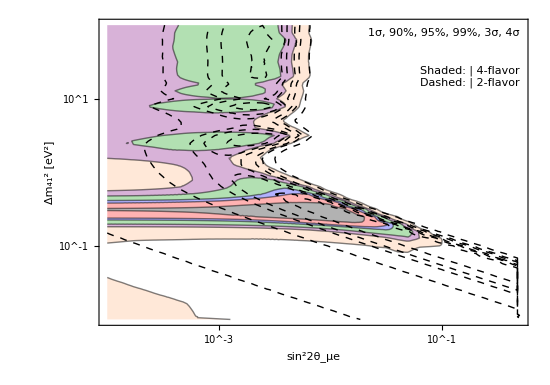
-Graphics-Brdar Kopp 2021

```mathematica
(* plots illustrating the impact of BG oscillations in MB *)
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
For[i=1,i≤2,i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-4,Log10[0.5]},Full,Full},Contours->MyContours,
ContourShading->If[MyTunes⟦i⟧=="default-nobgosc",None,MyFillingStyles],
ContourStyle->If[MyTunes⟦i⟧=="default-nobgosc",Directive[Black,Dashed],Directive[Thin,Black]]]
];
];
MyPlot[99]=Overlay[{JHEPPlot[Show[MyPlot[1],MyPlot[2],
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
Text[Style["1σ, 90%, 95%, 99%, 3σ, 4σ"],Scaled[{0.98,0.97}],{1,1},Background->GrayLevel[1,.7]],
Text[Style[Grid[{{"Shaded:","4-flavor"},{"Dashed:","2-flavor"}}]],Scaled[{0.98,0.85}],{1,1},Background->GrayLevel[1,.7]]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
Export["fig/mb-contours-s22thmue-default.pdf",MyPlot[99]];
```

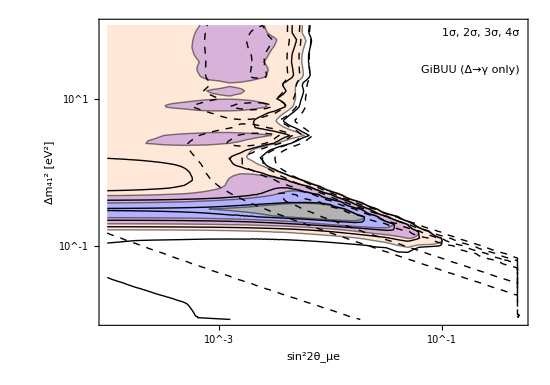
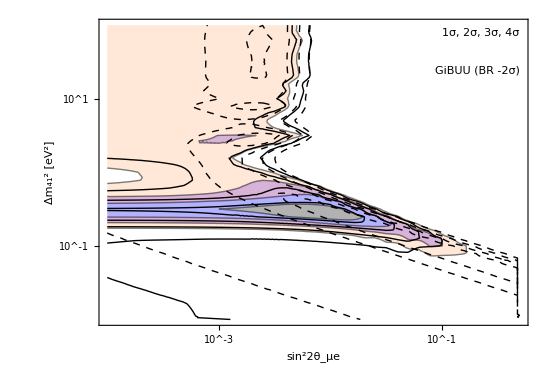
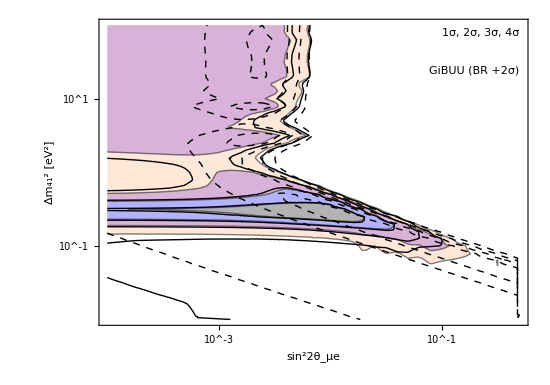
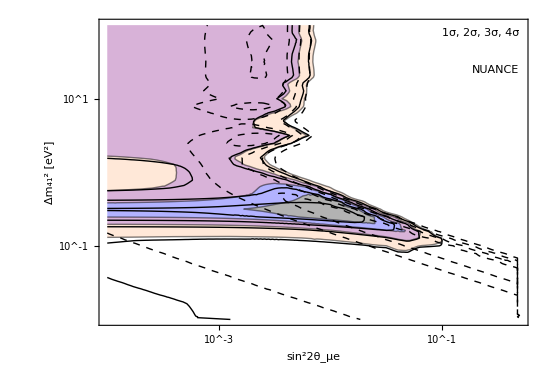
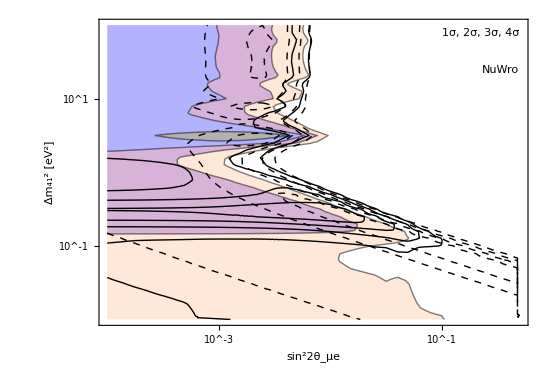
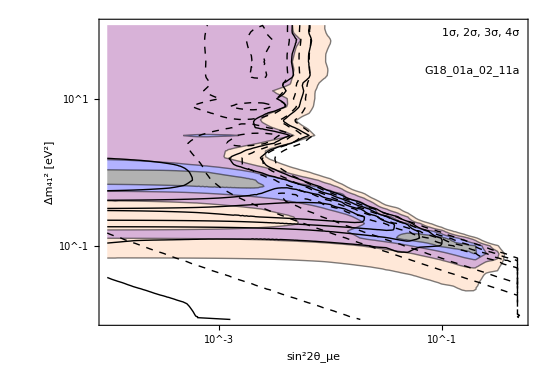
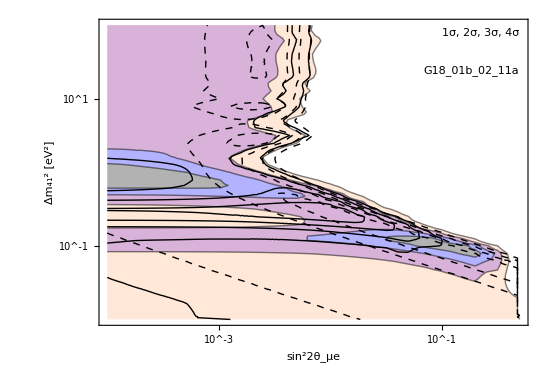
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
SmallPlots=True;
(*DataMB=Import["0-code/glb/mb-jk-2018/likihood_surface_contNu.txt","Table"];
Chi2MinMB=Min[DataMB⟦All,3⟧];
MBPlot=ListContourPlot[{Log10[#⟦2⟧],Log10[#⟦1⟧],#⟦3⟧-Chi2MinMB}&/@DataMB,Contours->MyContours,ContourShading->None,ContourStyle->Evaluate[Directive[Thick,Black]]];*)
MyContours={χ2[2,PValue[1]],χ2[2,PValue[2]],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[0,0,1,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-4,Log10[0.5]},Full,Full},Contours->MyContours,
ContourShading->If[MyTunes⟦i⟧=="default-nobgosc"||MyTunes⟦i⟧=="default",None,MyFillingStyles],
ContourStyle->Switch[MyTunes⟦i⟧,"default-nobgosc",Directive[Black,Dashed],"default",Directive[Black],_,Directive[Thin,Black]]]
];
];
For[i=1,i≤Length[DataFiles],i++,
MyPlot[200+i]=Overlay[{JHEPPlot[Show[MyPlot[i],MyPlot[1],MyPlot[2],
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
ImagePadding->If[SmallPlots,{{100,10},{80,15}},{{70,20},{60,15}}],PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
Text[Row[{Sequence@@Table[Style[ToString[j]<>"σ"<>If[j<4,", ",""],MyFillingStyles⟦j⟧,Opacity[.8]],{j,1,4}]}],Scaled[{0.98,0.97}],{1,1},Background->GrayLevel[1,.7]],
If[SmallPlots,
{Text[StringReplace[MyTunesHumanReadable⟦i⟧,"GENIE ":>""],Scaled[{0.98,0.85}],{1,1},Background->GrayLevel[1,.7]]},
(* Else *)
{Text[Style[Grid[{{"Solid:","MB (4-flavor)"},{"Shaded:",StringReplace[MyTunesHumanReadable⟦i⟧,"GENIE ":>""]}},Spacings->{0.2,Automatic},Alignment->Left]],Scaled[{0.98,0.8}],{1,1},Background->GrayLevel[1,.7]],
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven BG","MC-only BG"]],Scaled[{0.03,0.97}],{-1,1},Background->GrayLevel[1,.7]]}
]},BaseStyle->If[SmallPlots,{FontFamily->"Times",FontSize->28},{FontFamily->"Times",FontSize->18}]]],
Style[If[SmallPlots,"","Brdar Kopp 2021"],FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
If[MyTunes⟦i⟧≠"default"&&MyTunes⟦i⟧≠"default-nobgosc",
OutputSuffix=If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"dd","fp"];
Export["fig/mb-contours-s22thmue-"<>MyTunes⟦i⟧<>"-"<>OutputSuffix<>".pdf",MyPlot[200+i]];
];
];
Grid[{{MyPlot[203],MyPlot[204]},{MyPlot[205],MyPlot[206]},{MyPlot[207],MyPlot[208]},{MyPlot[209]}}]
```

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-4,Log10[0.5]},Full,Full},Contours->{χ2[2,0.01]},
ContourShading->Switch[MyTunes⟦i⟧,
"default",{GrayLevel[0,.3],None},
"default-nobgosc",{GrayLevel[0,.1],None},
_,None],
ContourStyle->Directive[If[MyTunes⟦i⟧=="default"||MyTunes⟦i⟧=="default-nobgosc",Black,{Thick,MyTuneColors⟦i⟧}],MyTuneLineStyles⟦i⟧]]
];
];
```

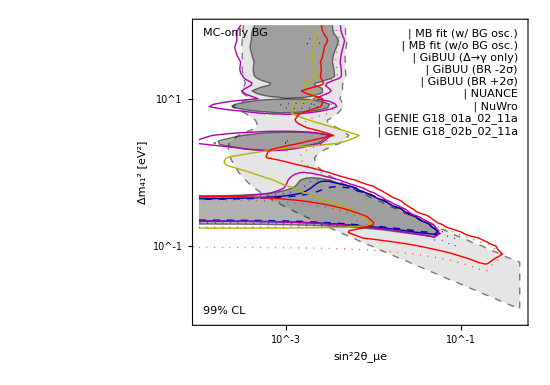
-Graphics-Brdar Kopp 2021

```mathematica
whichTunes=Flatten[Position[MyTunes,"default"|"default-nobgosc"|If[MySuffix=="-dd",{},"gibuu-brscan-max"|"gibuu-brscan-min"|"gibuu"]|"nuance"|"nuwro"|"G18_01a_02_11a"|"G18_02b_02_11a"]];
MyLegend=Framed[Grid[{
{LegendBox[GrayLevel[0,.3],MyTuneLineStyles⟦1⟧],"MB fit (w/ BG osc.)"},
{LegendBox[GrayLevel[0,.05],MyTuneLineStyles⟦2⟧],"MB fit (w/o BG osc.)"},
Sequence@@Table[{LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧]],MyTunesHumanReadable⟦i⟧},{i,whichTunes⟦3;;-1⟧}]
},Alignment->{Left,Center},Spacings->{Automatic,{0.1,{2->0.4,3->0.2}}},BaseStyle->{FontSize->16,FontFamily->"Times"}],Background->GrayLevel[1,.8]];
MyPlot[300]=Overlay[{JHEPPlot[Show[Sequence@@Table[MyPlot[i],{i,whichTunes}],
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven BG","MC-only BG"]],Scaled[{0.03,0.97}],{-1,1},Background->GrayLevel[1,.7]],
Text["99% CL",Scaled[{0.03,0.03}],{-1,-1}]
}
]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
OutputSuffix=If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"dd","fp"];
Export["fig/mb-contours-comparison-s22thmue-"<>OutputSuffix<>".pdf",MyPlot[300]];
```

### Exclusion Regions in U_μ4^2 and Δm^2

Evaluate “Exclusion Regions in sin^2 2 θ_μe and Δm^2” first to make sure definitions of labels, colors, line styles have been set.

```mathematica
DataFiles="3-3p1/mbbg/dm41s22thmueUm4-mbjk-"<>#<>MySuffix<>".dat"&/@MyTunes;
For[i=1,i≤Length[DataFiles],i++,
If[FileExistsQ[StringReplace[DataFiles⟦i⟧,".dat":>"-stripped.dat"]],
DataRaw[i]=KPImport[StringReplace[DataFiles⟦i⟧,".dat":>"-stripped.dat"],"Table"],
(* Else *)
DataRaw[i]=KPImport[DataFiles⟦i⟧,"Table"]
];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]=Select[Data[i],#⟦3⟧<0.75&]; (* select Subscript[U, μ4] range to avoid solutions with Subscript[U, μ4]~1 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[10^(#⟦2⟧)/(4*(10^(#⟦3⟧))^2)>0.2,1.*^12,#⟦4⟧]}&/@Data[i]; (* restrict Subscript[U, e4] range *)
Data[i]=Gather[Sort[Data[i]],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
Data[i]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Data[i], (* save χ^2 at optimum sin^2 2 Subscript[θ, μe] *)

(* Else - data files in dm41, th14, th24 *)
Print["Wrong file format!"];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
Um4Min[i]=Min[Data[i]⟦All,2⟧];
Um4Max[i]=Max[Data[i]⟦All,2⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
]; (* End[if] *)

Print[DataFiles⟦i⟧];
Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],Um4Min[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

3-3p1/mbbg/dm41s22thmueUm4-mbjk-default.dat

Best fit: sin^22θ_μe=1.77828, Δm^2=0.251189

χ_min^2=192.7, χ_(no osc)^2=211.77, Δχ_(no osc.)^2=19.0691 (CL 0.999928)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-default-nobgosc.dat

Best fit: sin^22θ_μe=5.30884, Δm^2=0.0398107

χ_min^2=188.602, χ_(no osc)^2=200.489, Δχ_(no osc.)^2=11.8877 (CL 0.997378)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-gibuu.dat

Best fit: sin^22θ_μe=1.88365, Δm^2=0.251189

χ_min^2=192.211, χ_(no osc)^2=216.767, Δχ_(no osc.)^2=24.5565 (CL 0.999995)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-gibuu-brscan-min.dat

Best fit: sin^22θ_μe=1.88365, Δm^2=0.316228

χ_min^2=194.416, χ_(no osc)^2=222.496, Δχ_(no osc.)^2=28.0805 (CL 0.999999)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-gibuu-brscan-max.dat

Best fit: sin^22θ_μe=1.88365, Δm^2=0.316228

χ_min^2=192.075, χ_(no osc)^2=213.219, Δχ_(no osc.)^2=21.1441 (CL 0.999974)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-nuance.dat

Best fit: sin^22θ_μe=1.6788, Δm^2=0.316228

χ_min^2=196.948, χ_(no osc)^2=216.295, Δχ_(no osc.)^2=19.3474 (CL 0.999937)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-nuwro.dat

Best fit: sin^22θ_μe=1.58489, Δm^2=3.16228

χ_min^2=219.354, χ_(no osc)^2=234.964, Δχ_(no osc.)^2=15.6099 (CL 0.999592)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_01a_02_11a.dat

Best fit: sin^22θ_μe=2.51189, Δm^2=0.125893

χ_min^2=195.399, χ_(no osc)^2=218.514, Δχ_(no osc.)^2=23.1146 (CL 0.99999)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_01b_02_11a.dat

Best fit: sin^22θ_μe=2.23872, Δm^2=0.794328

χ_min^2=195.458, χ_(no osc)^2=215.505, Δχ_(no osc.)^2=20.0472 (CL 0.999956)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_02a_02_11a.dat

Best fit: sin^22θ_μe=2.51189, Δm^2=0.125893

χ_min^2=192.682, χ_(no osc)^2=208.538, Δχ_(no osc.)^2=15.856 (CL 0.999639)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_02b_02_11a.dat

Best fit: sin^22θ_μe=2.66073, Δm^2=0.125893

χ_min^2=194.236, χ_(no osc)^2=211.698, Δχ_(no osc.)^2=17.4619 (CL 0.999838)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_10a_02_11a.dat

Best fit: sin^22θ_μe=1.6788, Δm^2=0.251189

χ_min^2=193.756, χ_(no osc)^2=204.92, Δχ_(no osc.)^2=11.1639 (CL 0.996235)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_10b_02_11a.dat

Best fit: sin^22θ_μe=1.33352, Δm^2=0.398107

χ_min^2=192.915, χ_(no osc)^2=210.84, Δχ_(no osc.)^2=17.9254 (CL 0.999872)

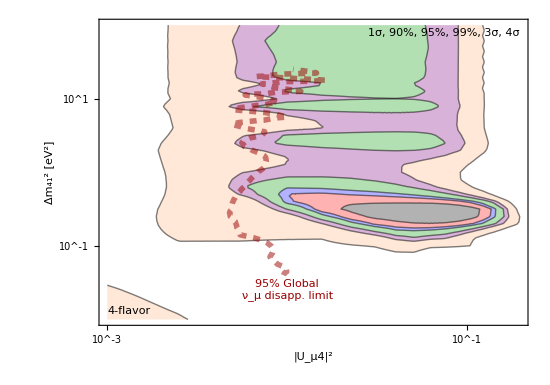
-Graphics-Brdar Kopp 2021

```mathematica
(* plots illustrating the impact of BG oscillations in MB *)
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
For[i=1,i≤2,i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,Sqrt[10^logUm4sq]]-Chi2Min[i],{logUm4sq,-3,Log10[Um4Max[i]^2]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{Full,Full,Full},Contours->MyContours,
ContourShading->If[MyTunes⟦i⟧=="default",MyFillingStyles,None],
ContourStyle->If[MyTunes⟦i⟧=="default",Directive[Thin,Black],Directive[Black,Dashed]]]
];
];
DataGlobalMu=Cases[Import["3-3p1/mbbg/mona/CombinedNuMuDis.dat","Table"],{Repeated[_?NumericQ]}];
MyPlotGlobalMu=cleanContourPlot[ListContourPlot[DataGlobalMu-Min[DataGlobalMu⟦All,3⟧],PlotRange->{Full,Full,Full},Contours->{χ2[2,0.05]},
ContourShading->None,ContourStyle->Directive[RGBColor[.6,0,0],AbsoluteThickness[4],Dashed]]];
MyPlot[99]=Overlay[{JHEPPlot[Show[MyPlot[1],(*MyPlot[2],*)MyPlotGlobalMu,
FrameLabel->{"|U_μ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
PlotRange->{{All,Log10[0.5]},All},ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
Text[Style["1σ, 90%, 95%, 99%, 3σ, 4σ"],Scaled[{0.98,0.97}],{1,1}(*,Background->GrayLevel[1,.7]*)],
Text["4-flavor",Scaled[{0.02,0.03}],{-1,-1},Background->GrayLevel[1,.7]],
Text[Style["95% Global\nν_μ disapp. limit",RGBColor[.6,0,0],LineSpacing->{0.9,0}],{-2,-1.45},{0,1},{1,0}]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
Export["fig/mb-contours-Um4sq-default.pdf",MyPlot[99]];
```

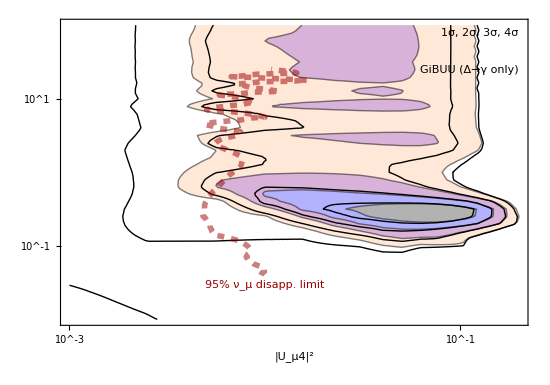
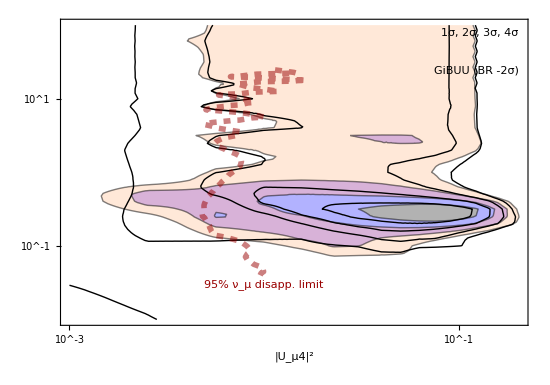
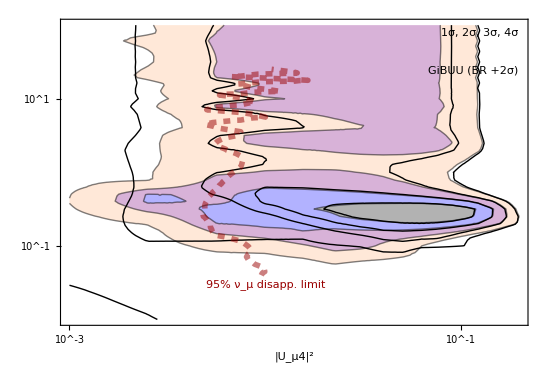
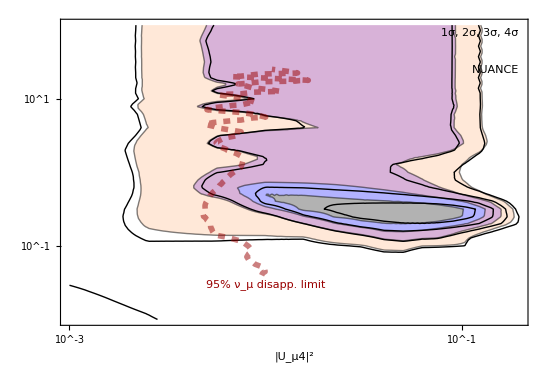
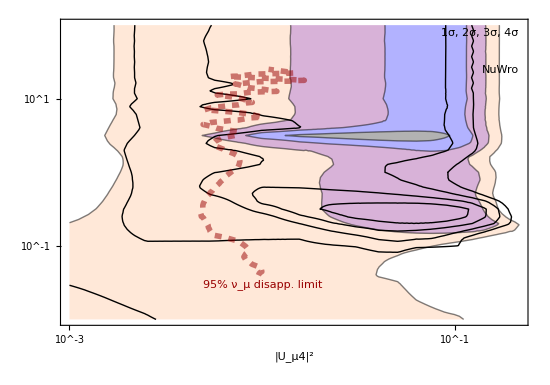
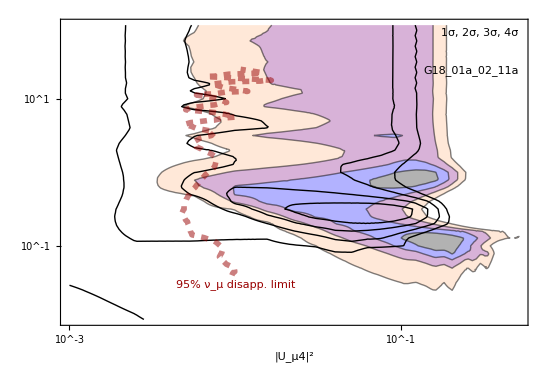
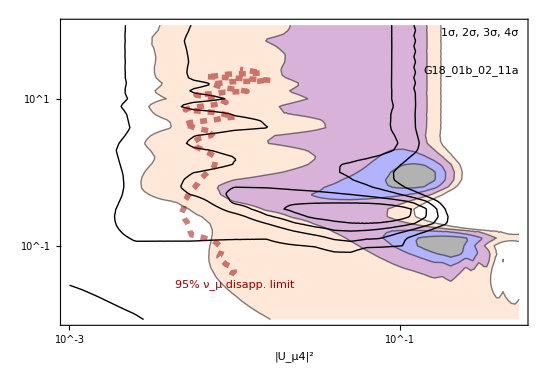
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
SmallPlots=True;
MyContours={χ2[2,PValue[1]],χ2[2,PValue[2]],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[0,0,1,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,Sqrt[10^logUm4sq]]-Chi2Min[i],{logUm4sq,-3,Log10[Um4Max[i]^2]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{Full,Full,Full},Contours->MyContours,
ContourShading->If[MyTunes⟦i⟧=="default-nobgosc"||MyTunes⟦i⟧=="default",None,MyFillingStyles],
ContourStyle->Switch[MyTunes⟦i⟧,"default-nobgosc",Directive[Black,Dashed],"default",Directive[Black],_,Directive[Thin,Black]]]
]
];
For[i=1,i≤Length[DataFiles],i++,
MyPlot[300+i]=Overlay[{JHEPPlot[Show[MyPlot[i],MyPlot[1],MyPlotGlobalMu,
FrameLabel->{"|U_μ4|^2",If[SmallPlots,"","Δm_41^2 [eV^2]"]},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
PlotRange->{{All,Log10[0.5]},All},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
ImagePadding->If[SmallPlots,{{100,10},{80,15}},{{70,20},{60,15}}],
Epilog->{
Text[Row[{Sequence@@Table[Style[ToString[j]<>"σ"<>If[j<4,", ",""],MyFillingStyles⟦j⟧,Opacity[.8]],{j,1,4}]}],Scaled[{0.98,0.97}],{1,1},Background->GrayLevel[1,.7]],
If[SmallPlots,
{Text[StringReplace[MyTunesHumanReadable⟦i⟧,"GENIE ":>""],Scaled[{0.98,0.85}],{1,1},Background->GrayLevel[1,.7]],
Text[Style["95% ν_μ disapp. limit",RGBColor[.6,0,0],Background->GrayLevel[1,.7]],{-2,-1.45},{0,1},{1,0}]},
(* Else *)
{Text[Style[Grid[{{"Solid:","MB (4-flavor)"},{"Shaded:",StringReplace[MyTunesHumanReadable⟦i⟧,"GENIE ":>""]}},Spacings->{0.2,Automatic},Alignment->Left]],Scaled[{0.98,0.8}],{1,1},Background->GrayLevel[1,.7]],
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven BG","MC-only BG"]],Scaled[{0.03,0.97}],{-1,1},Background->GrayLevel[1,.7]],
Text[Style["95% Global\nν_μ disapp. limit",RGBColor[.6,0,0],LineSpacing->{0.9,0},Background->GrayLevel[1,.7]],{-2,-1.45},{0,1},{1,0}]}
]},BaseStyle->If[SmallPlots,{FontFamily->"Times",FontSize->28},{FontFamily->"Times",FontSize->18}]]],Style[If[SmallPlots,"","Brdar Kopp 2021"],FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
If[MyTunes⟦i⟧≠"default"&&MyTunes⟦i⟧≠"default-nobgosc",
OutputSuffix=If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"dd","fp"];
Export["fig/mb-contours-Um4sq-"<>MyTunes⟦i⟧<>"-"<>OutputSuffix<>".pdf",MyPlot[300+i]];
];
];
Grid[{{MyPlot[303],MyPlot[304]},{MyPlot[305],MyPlot[306]},{MyPlot[307],MyPlot[308]},{MyPlot[309]}}]
```

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,Sqrt[10^logUm4sq]]-Chi2Min[i],{logUm4sq,-3,Log10[Um4Max[i]^2]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{Full,Full,Full},Contours->{χ2[2,0.01]},
ContourShading->Switch[MyTunes⟦i⟧,
"default",{GrayLevel[0,.3],None},
"default-nobgosc",{GrayLevel[0,.1],None},
_,None],
ContourStyle->Directive[If[MyTunes⟦i⟧=="default"||MyTunes⟦i⟧=="default-nobgosc",Black,{Thick,MyTuneColors⟦i⟧}],MyTuneLineStyles⟦i⟧]]
];
];
```

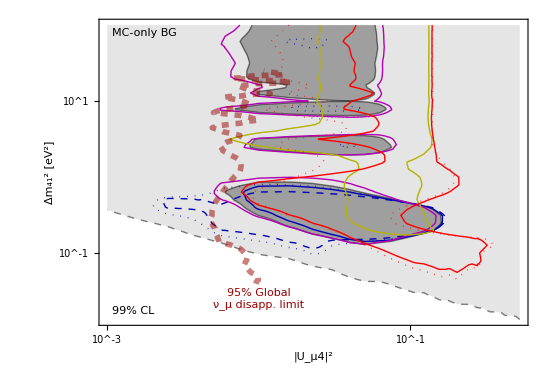
-Graphics-Brdar Kopp 2021

```mathematica
whichTunes=Flatten[Position[MyTunes,"default"|"default-nobgosc"|If[MySuffix=="-dd",{},"gibuu"|"gibuu-brscan-max"|"gibuu-brscan-min"]|"nuance"|"nuwro"|"G18_01a_02_11a"|"G18_02b_02_11a"]];
MyLegend=Framed[Grid[{
{LegendBox[GrayLevel[0,.3],MyTuneLineStyles⟦1⟧],"MB fit (w/ BG osc.)"},
{LegendBox[GrayLevel[0,.05],MyTuneLineStyles⟦2⟧],"MB fit (w/o BG osc.)"},
Sequence@@Table[{LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧]],MyTunesHumanReadable⟦i⟧},{i,whichTunes⟦3;;-1⟧}]
},Alignment->{Left,Center},Spacings->{Automatic,{0.1,{2->0.4,3->0.2}}},BaseStyle->{FontSize->16,FontFamily->"Times"}]];
MyPlot[300]=Overlay[{JHEPPlot[Show[Sequence@@Table[MyPlot[i],{i,whichTunes}],MyPlotGlobalMu,
FrameLabel->{"|U_μ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
PlotRange->{{All,Log10[0.5]},{-2,2}},ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven BG","MC-only BG"]],Scaled[{0.03,0.97}],{-1,1},Background->GrayLevel[1,.7]],
Text[Style["95% Global\nν_μ disapp. limit",RGBColor[.6,0,0],LineSpacing->{0.9,0}],{-2,-1.45},{0,1},{1,0}],
Text["99% CL",Scaled[{0.03,0.03}],{-1,-1}]
}
]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
OutputSuffix=If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"dd","fp"];
Export["fig/mb-contours-comparison-Um4sq-"<>OutputSuffix<>".pdf",MyPlot[300]];
```